# 3. izpit – Mathematica

## Računalniški praktikum 2023/24

Študijska smer : Finančna matematika, Matematika, Pedagoška matematika

## Podatki o študentu

Vpišite svoje podatke

Ime: David

Priimek: Šiška

Vpisna številka: 27241019

## Navodila

Čas reševanja za celoten izpit je 120 minut.
V tem delu izpita sta dve nalogi, ki sta skupaj vredni 30 točk od 100 možnih na izpitu.
Vsako nalogo rešujte v svojem razdelku. Pri vsaki nalogi je možna ena točka za pregledno napisano kodo.
Dovoljeno je uporabljati dokumentacijo o Mathematici in gradivo iz vaj.
Vsakršna komunikacija je prepovedana.

## 1. naloga [15 točk]

1. (5 točk) Izračunajte prvi odvod funkcije  2sin (2x+1)  cos (x).
2. (5 točk) Izračunajte vsoto  ∑_(k=1)^∞ (k^2+1)/k^4.
3. (5 točk) Izračunajte limito zaporedja .

```mathematica
D[2Sin[2x+1] Cos[x],x]
Sum[(k^2+1)/k^4,{k,1,Infinity}]
Limit[Tan[x]/x,x->0]
```

4 Cos[x] Cos[1+2 x]-2 Sin[x] Sin[1+2 x]

1/90 π^2 (15+π^2)

1

## 2. naloga [15 točk]

1. (5 točk) Definirajte funkciji x(t)=cos(3 t) in y(t)=2 sin(t).
2. (5 točk) Narišite parametrično podano krivuljo na območju t ∈[0,2π]. Namig: uporabite lahko funkcijo ParametricPlot.
3. (5 točk) S pomočjo ustrezne funkcije poiščite take vrednosti t ∈ [0, 2π], da velja x(t)=0. Namig: za dodajanje pogojev lahko uporabite && (“in”).

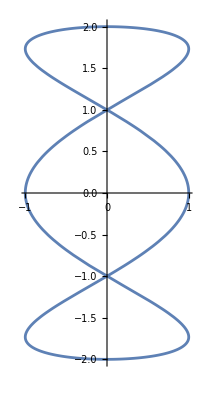

{{t→π/6},{t→π/2},{t→(5 π)/6},{t→(7 π)/6},{t→(3 π)/2},{t→(11 π)/6}}

```mathematica
x[t_]:=Cos[3t]
y[t_]:=2Sin[t]
ParametricPlot[{x[t],y[t]},{t,0,2Pi}]
Solve[x[t]==0&&0<=t<=2Pi,t]
```